```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

### J around other cusps

```mathematica
J1=Simplify[MirrorCurveJ2[-27/256,ur]]
```

-((8+9 ur) (512-576 ur+1080 ur^2+81 ur^3)^3)/(19683 ur^8 (64-80 ur+153 ur^2))

```mathematica
ur0=ur/.Solve[64-80 ur+153 ur^2==0,ur]
```

{8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
a1=FullSimplify[Series[J1,{ur,ur0[[2]],10}]];
```

```mathematica
a2=Series[8/153 (5+8 ⅈ √2)+Sum[a[i]q^i, {i,10}], {q,0,10}];
```

```mathematica
a3=Simplify[ComposeSeries[a1, a2]];
```

```mathematica
Series[1728KleinInvariantJ[Log[q]/(2Pi I)], {q,0,10}]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+333202640600 q^5+4252023300096 q^6+44656994071935 q^7+401490886656000 q^8+3176440229784420 q^9+22567393309593600 q^10+O[q]^11

```mathematica
sol=Simplify[Solve[a3-Series[1728KleinInvariantJ[Log[q]/(2Pi I)], {q,0,10}]==0,Array[a,10]]];
```

```mathematica
a3=a2/.First[sol]
```

8/153 (5+8 ⅈ √2)+(2048 (-6976-11369 ⅈ √2) q)/5688387+(16384 (1680185024+3039785485 ⅈ √2) q^2)/1903396862457+(8192 (-5850038733668800-12823968247666619 ⅈ √2) q^3)/636897527543599227+(131072 (623934858062410040896+1730410785263304691583 ⅈ √2) q^4)/213112918588891280945697+(4096 (-32285410263955807669386142400-119216980116040976696010842671 ⅈ √2) q^5)/71309926801947500408520618867+(851968 (225312627148995689010046635702080+1228127125030765062095451239775739 ⅈ √2) q^6)/23861085917126455059195492799705737+(16384 (-13273013073896587641852351287727748975808-136343966552091559733181103371477516558199 ⅈ √2) q^7)/7984181819815600253812463041202336363307+(1048576 (54101480085223225428904679341295683198080704+4531868742473204429610098951898257676160667629 ⅈ √2) q^8)/2671595062910317816528442070679754972862518577+(2048 (360861703099706899184578271967342901387604913880160192-4917997983752467773292580702819657484699438166773971597 ⅈ √2) q^9)/893945095595484354906398529712223491224500203568547+(32768 (-11483946860826203938932458566568074221676732563999415900864+72124473939190344808126337140617564106673048139677657976451 ⅈ √2) q^10)/33235984709144512831064990936170757180235693068475008913+O[q]^11

```mathematica
a3[[3]]
```

{8/153 (5+8 ⅈ √2),(2048 (-6976-11369 ⅈ √2))/5688387,(16384 (1680185024+3039785485 ⅈ √2))/1903396862457,(8192 (-5850038733668800-12823968247666619 ⅈ √2))/636897527543599227,(131072 (623934858062410040896+1730410785263304691583 ⅈ √2))/213112918588891280945697,(4096 (-32285410263955807669386142400-119216980116040976696010842671 ⅈ √2))/71309926801947500408520618867,(851968 (225312627148995689010046635702080+1228127125030765062095451239775739 ⅈ √2))/23861085917126455059195492799705737,(16384 (-13273013073896587641852351287727748975808-136343966552091559733181103371477516558199 ⅈ √2))/7984181819815600253812463041202336363307,(1048576 (54101480085223225428904679341295683198080704+4531868742473204429610098951898257676160667629 ⅈ √2))/2671595062910317816528442070679754972862518577,(2048 (360861703099706899184578271967342901387604913880160192-4917997983752467773292580702819657484699438166773971597 ⅈ √2))/893945095595484354906398529712223491224500203568547,(32768 (-11483946860826203938932458566568074221676732563999415900864+72124473939190344808126337140617564106673048139677657976451 ⅈ √2))/33235984709144512831064990936170757180235693068475008913}

```mathematica
Simplify[Series[(a j+b)/(c j+d)/.{j->1/q+744+aa1 q+aa2 q^2},{q,0,3}]][[3]]
```

{a/c,(b c-a d)/c^2,-((744 c+d) (b c-a d))/c^3,-((b c-a d) ((-553536+aa1) c^2-1488 c d-d^2))/c^4}

```mathematica
Simplify[(a j+b)/(c j+d)/.Solve[{
a/c==8/153 (5+8 ⅈ √2),
(b c-a d)/c^2==(2048 (-6976-11369 ⅈ √2))/5688387,
-((744 c+d) (b c-a d))/c^3==(16384 (1680185024+3039785485 ⅈ √2))/1903396862457,
a d-b c==1
},{a,b,c,d}]]
```

{(72 (908624 ⅈ-1452928 √2+243 (-5 ⅈ+8 √2) j))/(246845200 ⅈ+54784 √2-334611 ⅈ j),(72 (908624 ⅈ-1452928 √2+243 (-5 ⅈ+8 √2) j))/(246845200 ⅈ+54784 √2-334611 ⅈ j)}

```mathematica
Inverse[{{6,-1},{1,0}}]
```

{{0,1},{-1,6}}

```mathematica
-1/(tau-6)
```

-1/(-6+tau)

```mathematica
Simplify[NumeratorDenominator[PicardFuchsP2[el,ur]]/.{el->-27/256}]
```

{((8+9 ur)^2 (768-128 ur+1260 ur^2+4131 ur^3))/2048,(ur (8+9 ur)^3 (64-80 ur+153 ur^2))/4096}

```mathematica
Factor[NumeratorDenominator[PicardFuchsQ2[el,ur]]/.{el->-27/256}]
```

{((8+9 ur) (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/2048,(ur^2 (8+9 ur)^3 (64-80 ur+153 ur^2))/4096}

```mathematica
Factor[16384+32768 ur+73728 ur^2+401760 ur^3+676512 ur^4+334611 ur^5, Extension->Automatic]
```

(8+9 ur) (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4)

```mathematica
Simplify[PicardFuchsP2[el,ur]/.{el->-27/256}]
```

(2 (768-128 ur+1260 ur^2+4131 ur^3))/(ur (8+9 ur) (64-80 ur+153 ur^2))

```mathematica
Simplify[PicardFuchsQ2[el,ur]/.{el->-27/256}]
```

(2 (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/(ur^2 (8+9 ur)^2 (64-80 ur+153 ur^2))

```mathematica
PF[f_,ur_]:=D[f,{ur,3}]+(2 (768-128 ur+1260 ur^2+4131 ur^3))/(ur (8+9 ur) (64-80 ur+153 ur^2))D[f,{ur,2}]+(2 (2048+1792 ur+7200 ur^2+42120 ur^3+37179 ur^4))/(ur^2 (8+9 ur)^2 (64-80 ur+153 ur^2))D[f,{ur,1}];
```

```mathematica
Simplify[Series[PF[Log[ur]+Sum[a[i]ur^i, {i,1,30}],ur], {ur,0,20}]];
s2=Series[Log[ur]+Sum[a[i]ur^i, {i,1,30}],{ur,0,20}]/.First@Solve[Thread[%[[3,1;;20]]==0],Array[a,20]]
```

Log[ur]-(27 ur^2)/256-(27 ur^3)/128+(2187 ur^4)/131072+(2187 ur^5)/16384+(1366875 ur^6)/8388608-(295245 ur^7)/4194304-(4214031885 ur^8)/17179869184-(98972685 ur^9)/536870912+(641927052459 ur^10)/2748779069440+(138331435095 ur^11)/274877906944+(49684957439733 ur^12)/281474976710656-(25187626531683 ur^13)/35184372088832-(132624450992509047 ur^14)/126100789566373888+(4939250804555067 ur^15)/45035996273704960+(308655712675007143875 ur^16)/147573952589676412928+(2399996726641023939 ur^17)/1152921504606846976-(3791656653113811214161 ur^18)/2361183241434822606848-(6895785518346535409313 ur^19)/1180591620717411303424-(20818733654847363192290619 ur^20)/6044629098073145873530880+O[ur]^21

```mathematica
Simplify[Series[PF[1/2Log[ur]^2+Sum[a[i]ur^i, {i,1,5}]Log[ur]+Sum[b[i]ur^i, {i,1,5}],ur], {ur,0,8}]];
SolveAlways[%[[3,1;;9]]==0, Join[Array[a,5],Array[b,5]]]
```

{}

```mathematica
Simplify[PF[s3,ur]]
```

-81/(64 ur)-2889/512+(189 ur)/4096+(209115 ur^2)/65536+O[ur]^3

```mathematica
Simplify[F1Series2[el,ur,5,0]]
```

{{1/2 el ur^2 (2+4 ur+3 el ur^2+24 el ur^3),-ur/4+(1/16-el) ur^2-1/36 (1+90 el) ur^3-1/64 (-1+24 el+208 el^2) ur^4-1/300 (3-50 el+6450 el^2) ur^5},{2 el ur (1+3 ur+3 el ur^2+30 el ur^3),-1/4+(1/8-2 el) ur-1/12 (1+90 el) ur^2+(1/16-(3 el)/2-13 el^2) ur^3-1/60 (3-50 el+6450 el^2) ur^4},{2 el (1+6 ur+9 el ur^2+120 el ur^3),1/8-ur/6+(3 ur^2)/16-ur^3/5-el^2 ur^2 (39+430 ur)+el (-2-15 ur-(9 ur^2)/2+(10 ur^3)/3)}}

### GPT Frobenius

```mathematica
ClearAll[minPowerFromSeries];
minPowerFromSeries[expr_,u_Symbol,n_Integer]:=Module[{ser},ser=Series[expr,{u,0,n}];
If[Head[ser]===SeriesData,ser[[4]],0]];

ClearAll[linearSolveRules];
linearSolveRules[eqs_List,vars_List]:=Module[{poly,ca,mat,vec,solvec,r},(*turn eqs into linear expressions==0*)poly=(eqs/. Equal->Subtract);
ca=CoefficientArrays[poly,vars];
vec=-Normal[ca[[1]]];
mat=Normal[ca[[2]]];
Which[mat==={}||vars==={},{},Dimensions[mat][[1]]===Dimensions[mat][[2]],solvec=LinearSolve[mat,vec];
Thread[vars->solvec],True,(*overdetermined/rectangular:solve via normal equations*)solvec=LinearSolve[Transpose[mat].mat,Transpose[mat].vec];
Thread[vars->solvec]]];

ClearAll[seriesEqsUpTo];
seriesEqsUpTo[expr_,u_Symbol,n_Integer]:=Module[{kmin},kmin=minPowerFromSeries[expr,u,n];
Table[SeriesCoefficient[expr,{u,0,k}]==0,{k,kmin,n}]];

ClearAll[logSeriesEqsUpTo];
logSeriesEqsUpTo[expr_,u_Symbol,n_Integer,pmax_Integer]:=Module[{ser,poly},ser=Normal@Series[expr,{u,0,n}];
poly=Collect[ser,Log[u]];
Flatten@Table[seriesEqsUpTo[Coefficient[poly,Log[u],p],u,n],{p,0,pmax}]];


(*---main:Frobenius basis for rho^3=0---*)

ClearAll[FrobeniusBasisRho0Triple];
FrobeniusBasisRho0Triple[PFop_,u_Symbol,n_Integer?Positive]:=Module[{m,a,b,p,q,vars0,vars1,vars2,y0ans,y1ans,y2ans,eq0,eq1,eq2,sol0,sol1,sol2,y0full,y0tr,y1full,y2full},(*IMPORTANT:solve internally up to m=n+3*)m=n+3;
(*y0=1+a1 u+...+a_m u^m*)vars0=Array[a,m];
y0ans=1+Sum[a[k] u^k,{k,1,m}];
eq0=seriesEqsUpTo[PFop[y0ans,u],u,n];(*enforce up to u^n*)sol0=linearSolveRules[eq0,vars0];
y0full=Normal@Series[y0ans/. sol0,{u,0,m}];
y0tr=Normal@Series[y0full,{u,0,n}];
(*y1=Log[u] y0+(b1 u+...+b_m u^m) (no constant analytic term)*)vars1=Array[b,m];
y1ans=Log[u] y0full+Sum[b[k] u^k,{k,1,m}];
eq1=logSeriesEqsUpTo[PFop[y1ans,u],u,n,1];
sol1=linearSolveRules[eq1,vars1];
y1full=Normal@Series[y1ans/. sol1,{u,0,n}];
(*y2=1/2 Log[u]^2 y0+(p1 u+...+p_m u^m) Log[u]+(q1 u+...+q_m u^m) (no constants in Log-piece or analytic piece)*)vars2=Join[Array[p,m],Array[q,m]];
y2ans=1/2 Log[u]^2 y0full+(Sum[p[k] u^k,{k,1,m}]) Log[u]+Sum[q[k] u^k,{k,1,m}];
eq2=logSeriesEqsUpTo[PFop[y2ans,u],u,n,2];
sol2=linearSolveRules[eq2,vars2];
y2full=Normal@Series[y2ans/. sol2,{u,0,n}];
{Series[y0tr,{u,0,n}],Series[y1full,{u,0,n}],Series[y2full,{u,0,n}]}];


(*---run---*)
{y0,y1,y2}=FrobeniusBasisRho0Triple[PF,ur,10];

(*view as ordinary expressions*)
{Normal[y0],Normal[y1],Normal[y2]}
```

{1,-(27 ur^2)/256-(27 ur^3)/128+(2187 ur^4)/131072+(2187 ur^5)/16384+(1366875 ur^6)/8388608-(295245 ur^7)/4194304-(4214031885 ur^8)/17179869184-(98972685 ur^9)/536870912+(641927052459 ur^10)/2748779069440+Log[ur],ur/8+(ur^9 (-9454319796359-8978801983200 Log[ur]))/48704929136640+(ur^7 (-454288447-578680200 Log[ur]))/8220835840+(ur^3 (-1087-1944 Log[ur]))/9216+1/512 ur^2 (-43-54 Log[ur])+Log[ur]^2/2+(ur^4 (-4987+8748 Log[ur]))/524288+(ur^5 (874043+874800 Log[ur]))/6553600+(ur^6 (22298677+24603750 Log[ur]))/150994944-(7 ur^8 (25846755593+24080182200 Log[ur]))/687194767360+(ur^10 (45678132232597+44934893672130 Log[ur]))/192414534860800}

```mathematica
PF[y2,ur]
```

O[ur]^8

### Monodromies

```mathematica
u0=ur/.Solve[64-80 ur+153 ur^2==0,ur]
```

{8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
upath=Interpolation[{{0,I/10},{1/2-1/5,#+I/10}, {1/2,#-1/10}, {1/2+1/5,#-I/10}, {1,I/10}}&[-8/9], PeriodicInterpolation->True];
upath1[t_]:=(1-t)I/10+t (-8/9);
```

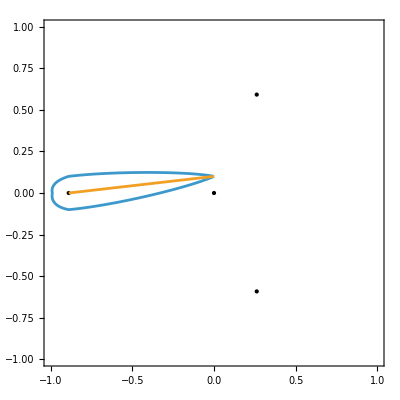

```mathematica
Show[{
Graphics[{Point[ReIm/@Join[u0, {0, -8/9}]]}],
ParametricPlot[Evaluate[ReIm/@{upath[t], upath1[t]}],{t,0,1}]
},
PlotRange->{{-1,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

```mathematica
Options[ComputeTransition2]={WorkingPrecision->60};
ComputeTransition2[el_,upath_,Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi,mon,SystMat,msg,tt=0},
Monitor[
msg="Integrating the connection...";
sol=NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA2[el,upath[t]].Psi[t],Psi[0]==IdentityMatrix[3]},Psi,{t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^7,StepMonitor:>(tt=t)];
mon=Psi[1]/. First[sol];
msg="Solving for the system matrix...";
SystMat=SystemMatrix2[F1Series2[el,upath[0],Nn,Nr],el,upath[0]];
LinearSolve[SystMat,mon.SystMat],msg<>" "<>ToString[Floor[100 tt]]<>"%."]];
```

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
mon2= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{-0.5,4.,-1.},{-1.5,9.,-2.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999999999999999159094809658, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(Ch[1,1]/.repCh).Sigma.{1,m,psi1[[1,2]],psi1[[1,3]]}
```

0.+0. ⅈ

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
mon1= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{0.,1.,-1.},{0.,0.,1.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999999999999999063544376405, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(Ch[0,0]/.repCh).Sigma.{1,m,psi1[[1,2]],psi1[[1,3]]}
```

0.+0. ⅈ

```mathematica
a1=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50];
monB= N[Chop[a1]]ᵀ
```

{{1.,0.,0.},{-1.33333+0.119331 ⅈ,6.,-1.},{-8.66667+0.596656 ⅈ,31.,-5.}}

```mathematica
With[{el=-27/256},
psi0=N[SystemMatrix2[F1Series2[el, upath1[0], 512,5], el, upath1[0]],100];
a1=NDSolve[{Psi'[t]==upath1'[t]*PicardFuchsA2[el,upath1[t]].Psi[t],Psi[0]==psi0},Psi,{t,0,1},WorkingPrecision->40,MaxSteps->10^7];
psi1=Psi[1]/.First[a1];
]
```

NDSolve::ndsz: At t == 0.9999999999999999998107022866345453149181, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Psi[.9999999999999999]/.First[a1]
```

{{1.,0.666667+0.119331 ⅈ,2.+0.715987 ⅈ},{0.,1.97471+105.748 ⅈ,-80.7197+583.323 ⅈ},{0.,-2.48934×10^16-1.89376×10^17 ⅈ,2.70898×10^16-1.06313×10^18 ⅈ}}

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[{m+1/2,1+6m}]
]
```

{0.666667+0.119331 ⅈ,2.+0.715987 ⅈ}

```mathematica
MatrixForm[monB]
```

(1. | 0. | 0.
-1.33333+0.119331 ⅈ | 6. | -1.
-8.66667+0.596656 ⅈ | 31. | -5.)

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[{-3/2+m, -19/2+5m}]
]
```

{-1.33333+0.119331 ⅈ,-8.66667+0.596656 ⅈ}

```mathematica
mB={{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}};
```

```mathematica
MatrixForm[MonodromyFromSphericalTwist[Ch[2,1]/.repCh]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-3/2 | 1 | 6 | -1
-15/2 | 5 | 25 | -4)

```mathematica
Tr[monB]
```

2.

```mathematica
MatrixForm[MatrixPower[mB,3]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 2 | -1 | 0
2 | 12 | 0 | -1)

```mathematica
Chop[MatrixPower[monB,3]]
```

{{1.,0,0},{1.33333+0.238662 ⅈ,-1.,0},{4.+1.43197 ⅈ,0,-1.}}

```mathematica
MatrixForm[MonodromyFromSphericalTwist[Ch[p,q]/.repCh][[{1,3,4},{1,3,4}]]]
```

(1 | 0 | 0
-p q+q^2/2 | 1+2 p+q | -1
(2 p+q) (-p q+q^2/2) | (2 p+q)^2 | 1-2 p-q)

```mathematica
MatrixForm[mon2]
```

(1. | 0. | 0.
-0.5 | 4. | -1.
-1.5 | 9. | -2.)

```mathematica
mB
```

{{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}}

```mathematica
Dot@@(MonodromyFromSphericalTwist/@{GV[0,1,1/2],Ch[2,1]}/.repCh)
```

{{1,0,0,0},{0,1,0,0},{-3/2,1,6,-1},{-19/2,5,31,-5}}

```mathematica
Solve[{1+2 p+q==6, -p q+q^2/2==-3/2},{p,q}]
```

{{p→2,q→1},{p→7/4,q→3/2}}

```mathematica
MatrixForm[Inverse[MLV]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1 | 0 | 1 | 0
4 | -1 | -8 | 1)

```mathematica
With[{m=Log[-27/256]/(2Pi I)/3},
N[4-m]
]
```

3.83333-0.119331 ⅈ

```mathematica
MatrixForm[Chop[mon1.mon2.monB]]
```

(1. | 0 | 0
-1. | 1. | 0
3.83333-0.119331 ⅈ | -8. | 1.)

### Important el values

```mathematica
PolyJ[el_,ur_, j_]=#[[1]]-j#[[2]]&@NumeratorDenominator[MirrorCurveJ[el,ur]]
```

(1-8 el ur^2-24 ur^3+16 el^2 ur^4)^3-j ur^8 (el+ur-8 el^2 ur^2-36 el ur^3-27 ur^4+16 el^3 ur^4)

```mathematica
FullSimplify[Resultant[PolyJ[el,ur,j],D[PolyJ[el,ur,j],ur], ur]]
```

-(27+256 el^3)^3 (-1728+j)^6 j^8 (4096 el^6+27 j-16 el^3 j) ((27+256 el^3) (243+256 el^3)^3-16777216 el^9 j)

```mathematica
Solve[4096 el^6+27 j-16 el^3 j==0,j]
Solve[MirrorCurveJ[el,ur]-j==0/.First[%],ur]
```

{{j→(4096 el^6)/(-27+16 el^3)}}

-(4096 el^6)/(-27+16 el^3)+((1-8 el ur^2-24 ur^3+16 el^2 ur^4)^3)/(ur^8 (el+ur-8 el^2 ur^2-36 el ur^3-27 ur^4+16 el^3 ur^4))

```mathematica
Solve[(27+256 el^3) (243+256 el^3)^3-16777216 el^9 j==0,j]
```

{{j→((27+256 el^3) (243+256 el^3)^3)/(16777216 el^9)}}

```mathematica
Simplify[Discriminant[PolyJ[el,ur,j],ur]]
```

-(27+256 el^3)^3 (387420489+4897760256 el^3+12899450880 el^6+4294967296 el^12-16777216 el^9 (-756+j)) (-1728+j)^6 j^8

```mathematica
Simplify@Solve[(387420489+4897760256 el^3+12899450880 el^6+4294967296 el^12-16777216 el^9 (-756+j))==0,j]
```

{{j→((27+256 el^3) (243+256 el^3)^3)/(16777216 el^9)}}

```mathematica
Solve[{1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4==0,D[1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4,ur]==0},{el, ur}]
```

{{el→-27/256,ur→-8/9}}

### solving PF near ur = -8/9

```mathematica
Simplify[ExpandAll[PicardFuchsQ2[el,ur]]]
```

(8+16 ur+(9-256 el) ur^2-1860 el ur^3+16 el (-189+64 el) ur^4+54 el (-27+16 el) ur^5)/(ur^2 (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))

```mathematica
Simplify[ExpandAll[PicardFuchsP2[el,z+(-8/9)]]]
```

(32 el^2 (8-9 z)^4 (4+27 z)+729 (8+18 z+243 z^2)-54 el (8-9 z)^2 (-32-144 z-1134 z^2+2187 z^3))/(z (-8+9 z) (16 el^2 (8-9 z)^4+729 (1+9 z)-27 el (8-9 z)^2 (-8-36 z+81 z^2)))

```mathematica
Simplify[Series[PicardFuchs2[(ur+8/9)^r, -27/256, ur], {ur,-8/9,1}]]
```

(8/9+ur)^r (((35 r)/36-2 r^2+r^3)/(ur+8/9)^3+((395-684 r) r)/(144 (ur+8/9)^2)+1/O[ur+8/9])

```mathematica
Solve[(35 r)/36-2 r^2+r^3==0,r]
```

{{r→0},{r→5/6},{r→7/6}}

```mathematica
(ur+8/9)+Sum[If[i==3,Nothing,a[i](ur+8/9)^i], {i,2,7}]
```

8/9+Nothing+ur+(8/9+ur)^2 a[2]+(8/9+ur)^4 a[4]+(8/9+ur)^5 a[5]+(8/9+ur)^6 a[6]+(8/9+ur)^7 a[7]

```mathematica
(ur+8/9)+Sum[If[i==3,0,a[i](ur+8/9)^i], {i,2,13}]
pi=Series[%, {ur,-8/9,13}]
```

8/9+ur+(8/9+ur)^2 a[2]+(8/9+ur)^4 a[4]+(8/9+ur)^5 a[5]+(8/9+ur)^6 a[6]+(8/9+ur)^7 a[7]+(8/9+ur)^8 a[8]+(8/9+ur)^9 a[9]+(8/9+ur)^10 a[10]+(8/9+ur)^11 a[11]+(8/9+ur)^12 a[12]+(8/9+ur)^13 a[13]

(ur+8/9)+a[2] (ur+8/9)^2+a[4] (ur+8/9)^4+a[5] (ur+8/9)^5+a[6] (ur+8/9)^6+a[7] (ur+8/9)^7+a[8] (ur+8/9)^8+a[9] (ur+8/9)^9+a[10] (ur+8/9)^10+a[11] (ur+8/9)^11+a[12] (ur+8/9)^12+a[13] (ur+8/9)^13+O[ur+8/9]^14

```mathematica
Simplify[PicardFuchs2[pi,el, ur]][[3,1;;7]];
sol=Simplify[Solve[Thread[%==0],Table[If[i==3,Nothing,a[i]],{i,2,8}]]]
```

{{a[2]→(9 (27+512 el))/(432+4096 el),a[4]→-(729 (-45927-559872 el-4423680 el^2+67108864 el^3))/(1024 (27+256 el)^3),a[5]→-(6561 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4))/(40960 (27+256 el)^4),a[6]→-(531441 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5))/(131072 (27+256 el)^5),a[7]→-1/(3670016 (27+256 el)^6)531441 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6),a[8]→-1/(33554432 (27+256 el)^7)4782969 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7)}}

```mathematica
(ur+8/9)^3+Sum[a[i](ur+8/9)^i, {i,4,14}];
pi2=Series[%, {ur,-8/9,14}]
```

(ur+8/9)^3+a[4] (ur+8/9)^4+a[5] (ur+8/9)^5+a[6] (ur+8/9)^6+a[7] (ur+8/9)^7+a[8] (ur+8/9)^8+a[9] (ur+8/9)^9+a[10] (ur+8/9)^10+a[11] (ur+8/9)^11+a[12] (ur+8/9)^12+a[13] (ur+8/9)^13+a[14] (ur+8/9)^14+O[ur+8/9]^15

```mathematica
Simplify[PicardFuchs2[pi2, el, ur]][[3,1;;7]];
sol2=Simplify@Solve[Thread[%==0],Table[a[i],{i,4,10}]]
```

{{a[4]→(27 (-99+1024 el))/(864+8192 el),a[5]→(243 (36207-211968 el+1310720 el^2))/(640 (27+256 el)^2),a[6]→(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3))/(2048 (27+256 el)^3),a[7]→(19683 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4))/(57344 (27+256 el)^4),a[8]→(177147 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5))/(524288 (27+256 el)^5),a[9]→1/(1048576 (27+256 el)^6)531441 (26338781944665-108735447541248 el+1047757897728 el^2+1146819660742656 el^3-3174865595006976 el^4-3324923162394624 el^5+31525197391593472 el^6),a[10]→1/(83886080 (27+256 el)^7)43046721 (-5066485633590165+18262870479244800 el+33734144410140672 el^2-425714076069396480 el^3+1682514386217861120 el^4-3427402044149858304 el^5-141863388262170624 el^6+11529215046068469760 el^7)}}

```mathematica
piS=Series[pi/.First[sol],{ur,-8/9,8}]
```

(ur+8/9)+(9 (27+512 el) (ur+8/9)^2)/(432+4096 el)-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) (ur+8/9)^4)/(1024 (27+256 el)^3)-(6561 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) (ur+8/9)^5)/(40960 (27+256 el)^4)-(531441 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) (ur+8/9)^6)/(131072 (27+256 el)^5)-1/(3670016 (27+256 el)^6)531441 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6) (ur+8/9)^7-1/(33554432 (27+256 el)^7)4782969 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7) (ur+8/9)^8+O[ur+8/9]^9

```mathematica
pi2S=Series[pi2/.First[sol2], {ur,-8/9, 10}]
```

(ur+8/9)^3+(27 (-99+1024 el) (ur+8/9)^4)/(864+8192 el)+(243 (36207-211968 el+1310720 el^2) (ur+8/9)^5)/(640 (27+256 el)^2)+(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3) (ur+8/9)^6)/(2048 (27+256 el)^3)+(19683 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4) (ur+8/9)^7)/(57344 (27+256 el)^4)+(177147 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5) (ur+8/9)^8)/(524288 (27+256 el)^5)+1/(1048576 (27+256 el)^6)531441 (26338781944665-108735447541248 el+1047757897728 el^2+1146819660742656 el^3-3174865595006976 el^4-3324923162394624 el^5+31525197391593472 el^6) (ur+8/9)^9+1/(83886080 (27+256 el)^7)43046721 (-5066485633590165+18262870479244800 el+33734144410140672 el^2-425714076069396480 el^3+1682514386217861120 el^4-3427402044149858304 el^5-141863388262170624 el^6+11529215046068469760 el^7) (ur+8/9)^10+O[ur+8/9]^11

```mathematica
{{1,0,0},{T0,a,b},{TD0,c,d}}.{1,pi/.{a->A},pi2/.{a->B}}
tau0=Simplify[Series[D[%[[3]],ur]/D[%[[2]],ur],{ur,-8/9,4}]]
```

{1,T0+a (ur+8/9)+a A[2] (ur+8/9)^2+b (ur+8/9)^3+(a A[4]+b B[4]) (ur+8/9)^4+(a A[5]+b B[5]) (ur+8/9)^5+(a A[6]+b B[6]) (ur+8/9)^6+(a A[7]+b B[7]) (ur+8/9)^7+(a A[8]+b B[8]) (ur+8/9)^8+(a A[9]+b B[9]) (ur+8/9)^9+(a A[10]+b B[10]) (ur+8/9)^10+(a A[11]+b B[11]) (ur+8/9)^11+(a A[12]+b B[12]) (ur+8/9)^12+(a A[13]+b B[13]) (ur+8/9)^13+O[ur+8/9]^14,TD0+c (ur+8/9)+c A[2] (ur+8/9)^2+d (ur+8/9)^3+(c A[4]+d B[4]) (ur+8/9)^4+(c A[5]+d B[5]) (ur+8/9)^5+(c A[6]+d B[6]) (ur+8/9)^6+(c A[7]+d B[7]) (ur+8/9)^7+(c A[8]+d B[8]) (ur+8/9)^8+(c A[9]+d B[9]) (ur+8/9)^9+(c A[10]+d B[10]) (ur+8/9)^10+(c A[11]+d B[11]) (ur+8/9)^11+(c A[12]+d B[12]) (ur+8/9)^12+(c A[13]+d B[13]) (ur+8/9)^13+O[ur+8/9]^14}

c/a+(3 (-b c+a d) (ur+8/9)^2)/a^2+(2 (b c-a d) (3 A[2]-2 B[4]) (ur+8/9)^3)/a^2+((-b c+a d) (-9 b+a (12 A[2]^2-8 A[2] B[4]+5 B[5])) (ur+8/9)^4)/a^3+O[ur+8/9]^5

```mathematica
Simplify[Series[J[tau0], {ur,-8/9,4}]]
```

J[c/a]+(3 (-b c+a d) J'[c/a] (ur+8/9)^2)/a^2+(2 (b c-a d) (3 A[2]-2 B[4]) J'[c/a] (ur+8/9)^3)/a^2+((b c-a d) (-2 a (-9 b+a (12 A[2]^2-8 A[2] B[4]+5 B[5])) J'[c/a]+9 (b c-a d) J''[c/a]) (ur+8/9)^4)/(2 a^4)+O[ur+8/9]^5

```mathematica
Simplify[Series[MirrorCurveJ2[el,ur], {ur,-8/9,3}]]
```

((27+256 el) (243+256 el)^3)/(16777216 el^3)-(6561 ((243+256 el)^2 (-19683-124416 el+65536 el^2)) (ur+8/9)^2)/(268435456 (el^3 (27+256 el)))-(59049 ((243+256 el)^2 (1240029+2799360 el-35979264 el^2+16777216 el^3)) (ur+8/9)^3)/(1073741824 (el^3 (27+256 el)^2))+O[ur+8/9]^4

```mathematica
Simplify[Solve[J[c/a]==((27+256 el) (243+256 el)^3)/(16777216 el^3),J[c/a]]]
```

{{J[c/a]→((27+256 el) (243+256 el)^3)/(16777216 el^3)}}

```mathematica
Simplify[Solve[-(6561 ((243+256 el)^2 (-19683-124416 el+65536 el^2)) (ur+8/9)^2)/(268435456 (el^3 (27+256 el)))==(3 (-b c+a d) J'[c/a] (ur+8/9)^2)/a^2, J'[c/a]]]
```

{{J'[c/a]→(2187 a^2 (243+256 el)^2 (-19683-124416 el+65536 el^2))/(268435456 (b c-a d) el^3 (27+256 el))}}

```mathematica
Simplify[((2187 a^2 (243+256 el)^2 (-19683-124416 el+65536 el^2))/(268435456 (b c-a d) el^3 (27+256 el)))/(((27+256 el) (243+256 el)^3)/(16777216 el^3))]
```

(2187 a^2 (-19683-124416 el+65536 el^2))/(16 (b c-a d) (27+256 el)^2 (243+256 el))

```mathematica
a1=Simplify[A[el]+B[el]piS+C1[el]pi2S]
```

A[el]+B[el] (ur+8/9)+(9 (27+512 el) B[el] (ur+8/9)^2)/(432+4096 el)+C1[el] (ur+8/9)^3+(-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) B[el])/(1024 (27+256 el)^3)+(27 (-99+1024 el) C1[el])/(864+8192 el)) (ur+8/9)^4-1/(40960 (27+256 el)^4)243 (27 (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B[el]-64 (27+256 el)^2 (36207-211968 el+1310720 el^2) C1[el]) (ur+8/9)^5-1/(131072 (27+256 el)^5)729 (729 (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B[el]-64 (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1[el]) (ur+8/9)^6-1/(3670016 (27+256 el)^6)19683 (27 (817844652279+9924494865408 el+179938632646656 el^2-1193161368010752 el^3+3400299838439424 el^4-6649846324789248 el^5+55169095435288576 el^6) B[el]-64 (27+256 el)^2 (1122934833-5842544256 el+17211211776 el^2-59190018048 el^3+300647710720 el^4) C1[el]) (ur+8/9)^7-1/(33554432 (27+256 el)^7)177147 (27 (-152020313099199-1933330863492864 el-33802251575869440 el^2+210736492144754688 el^3-489734759396671488 el^4+522606672774955008 el^5-1915155741539303424 el^6+23058430092136939520 el^7) B[el]-64 (27+256 el)^2 (-208503967617+974314168704 el-1458820399104 el^2+1459517128704 el^3-20564303413248 el^4+123145302310912 el^5) C1[el]) (ur+8/9)^8+O[ur+8/9]^9

```mathematica
ClearAll[A1,A2];
A1[f_]:=-2 m u^3 D[f,{m,0},{u,1}]-m u^4 D[f,{m,0},{u,2}]+1/3 m D[f,{m,1},{u,0}]+1/3 m u D[f,{m,1},{u,1}]+1/3 m^2 D[f,{m,2},{u,0}];
A2[f_]:=1/9 u D[f,{m,0},{u,1}]+1/9 u^2 D[f,{m,0},{u,2}]+4/9 m D[f,{m,1},{u,0}]-4/9 m u D[f,{m,1},{u,1}]-u^2 D[f,{m,1},{u,1}]+4/9 m^2 D[f,{m,2},{u,0}];
```

```mathematica
Simplify[A1[f[m^3, u/m]]/.{m->el^(1/3), u->ur el^(1/3)}]
```

el (-2 ur^3 f^(0,1)[el,ur]-ur^4 f^(0,2)[el,ur]+3 f^(1,0)[el,ur]-ur f^(1,1)[el,ur]+3 el f^(2,0)[el,ur])

```mathematica
Simplify[A2[f[m^3, u/m]]/.{m->el^(1/3), u->ur el^(1/3)}]
```

ur (1+ur) f^(0,1)[el,ur]+ur^2 (1+ur) f^(0,2)[el,ur]+el (4 f^(1,0)[el,ur]-ur (4+3 ur) f^(1,1)[el,ur]+4 el f^(2,0)[el,ur])

```mathematica
ClearAll[PF1,PF2];
PF1[f_,el_,ur_]:=(-2 ur^3 D[f,ur]-ur^4 D[f,{ur,2}]+3 D[f,el]-ur D[f,el,ur]+3 el D[f,{el,2}]);
PF2[f_,el_,ur_]:=ur (1+ur) D[f,ur]+ur^2 (1+ur) D[f,{ur,2}]+el (4 D[f,el]-ur (4+3 ur) D[f,ur,el]+4 el D[f,{el,2}]);
```

```mathematica
eqns={
512 B[el]+3 (27+256 el) (27 A'[el]+8 B'[el]+27 el A''[el])==0,
20736 (729+3456 el+32768 el^2) B[el]+(27+256 el) (-8192 (27+256 el) C1[el]+2187 ((81+1024 el) B'[el]+3 el (27+256 el) B''[el]))==0,
20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el])==0
}
```

```mathematica
(6 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)^4+1/(864 (27+256 el)^3)(-4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el]+81 (-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el])))
```

```mathematica
temp=Simplify[First@Solve[20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el])==0,C1'[el]]]
Simplify[D[C1'[el]/.temp,el]]
Simplify[81 ((64 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el]))==4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el]/.{C1''[el]->%}]
```

{C1'[el]→(20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]))/(192 (27+256 el)^3)}

-(6912 (-8019+124416 el+1441792 el^2) B[el])/(27+256 el)^4+1/(192 (27+256 el)^3)(23068672 (27+256 el) C1[el]+10368 (243+183168 el+720896 el^2) B'[el]+(27+256 el) (-90112 (27+256 el) C1'[el]+243 (243+1152 el+65536 el^2) B''[el]))

(10368 (6436341+255301632 el+386187264 el^2-11324620800 el^3+4294967296 el^4) B[el])/(27+256 el)+27 (27+256 el) (64 (-8019-31104 el+425984 el^2) C1'[el]+243 el (243+1152 el+65536 el^2) B''[el])==8192 (754515+2301696 el-44236800 el^2+16777216 el^3) C1[el]+4374 (-45927-575424 el-16146432 el^2+20971520 el^3) B'[el]

```mathematica
temp1
```

{(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0,81 ((256 (729+3456 el+32768 el^2) B[el])/(27+256 el)+27 (81+1024 el) B'[el]+81 el (27+256 el) B''[el])==8192 (27+256 el) C1[el],81 ((256 (-45927-2426112 el-16809984 el^2+16777216 el^3) B[el])/(27+256 el)+27 (729+62208 el+131072 el^2) B'[el]+(27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el]))==8192 (-15309-131328 el+131072 el^2) C1[el],81 ((64 (6436341+227587968 el+816168960 el^2-6341787648 el^3+4294967296 el^4) B[el])/(27+256 el)-27 (-45927-559872 el-4423680 el^2+67108864 el^3) B'[el]+32 (27+256 el)^2 ((-99+1024 el) C1'[el]+el (27+256 el) C1''[el]))==4096 (754515+4354560 el-24772608 el^2+16777216 el^3) C1[el],(5184 (4570924041+211472892288 el+1772922028032 el^2+2605115768832 el^3+5798205849600 el^4-4398046511104 el^5) B[el])/(27+256 el)+4096 (-565276077-5974394112 el-8408530944 el^2-22649241600 el^3+17179869184 el^4) C1[el]+4374 (13286025+204493248 el+2884460544 el^2+7587495936 el^3+98784247808 el^4) B'[el]==243 (27+256 el) (96 (225261+1810944 el+3997696 el^2+67108864 el^3) C1'[el]-27 el (-45927-559872 el-4423680 el^2+67108864 el^3) B''[el]+32 el (27+256 el)^2 (-99+1024 el) C1''[el]),8192 (247781709045+2646173702016 el-1299512180736 el^2-39740246065152 el^3-5798205849600 el^4+10995116277760 el^5) C1[el]+2187 (-24063117039-404904189312 el-4886204497920 el^2+3864866586624 el^3+99265284145152 el^4+483785116221440 el^5) B'[el]==1/(27+256 el)20736 (1007766785331+47186450819712 el+353710199070720 el^2-531374819770368 el^3-5266785787969536 el^4-742170348748800 el^5+1407374883553280 el^6) B[el]+81 (27+256 el) (64 (-888037911-7553233152 el+11816534016 el^2+106602430464 el^3+687194767360 el^4) C1'[el]-81 el (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B''[el]+192 el (27+256 el)^2 (36207-211968 el+1310720 el^2) C1''[el]),8192 (-18176348802087-205517979202176 el+51671007903744 el^2+2275559451131904 el^3-11256578854354944 el^4+1009351674298368 el^5+1125899906842624 el^6) C1[el]+2187 (1758243319245+31202610224256 el+401436393652224 el^2+274885578326016 el^3-4475809041481728 el^4+27311868833955840 el^5+79938893385826304 el^6) B'[el]==1/(27+256 el)20736 (-73872176581053-3548649541343616 el-27829452534718464 el^2+26985568684474368 el^3+197681174619881472 el^4-1461682236750299136 el^5+129197014310191104 el^6+144115188075855872 el^7) B[el]+81 (27+256 el) (64 (65148820749+628500549888 el-531672367104 el^2-4046287011840 el^3+30227979829248 el^4+109951162777600 el^5) C1'[el]-729 el (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B''[el]+64 el (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1''[el])}

```mathematica
20736 (-45927-2426112 el-16809984 el^2+16777216 el^3) B[el]+(27+256 el) (-8192 (-15309-131328 el+131072 el^2) C1[el]+81 (27 (729+62208 el+131072 el^2) B'[el]+(27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el])))/.temp//Simplify
```

-54 (20736 (1215+53568 el+360448 el^2) B[el]+(27+256 el) (-90112 (27+256 el) C1[el]+243 (243+1152 el+65536 el^2) B'[el]-192 (27+256 el)^2 C1'[el]))

```mathematica
Simplify[PF1[a1,el,ur]][[3]];
temp1=Simplify[Thread[%==0]];
```

gpt

```mathematica
gpteqns={
el (256 el+27)^2 B''[el]+(256 el+27) (512 el+27) B'[el]+(16384 el+1920) B[el]==0,
C1[el]==(81/(64 (256 el+27)^2))*((65536 el^2-3456 el+243) B[el]-(27648 el^2+2916 el) B'[el]),
(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0
}
```

{(1920+16384 el) B[el]+(27+256 el) (27+512 el) B'[el]+el (27+256 el)^2 B''[el]==0,C1[el]==(81 ((243-3456 el+65536 el^2) B[el]-(2916 el+27648 el^2) B'[el]))/(64 (27+256 el)^2),(512 B[el])/(27+256 el)+81 A'[el]+24 B'[el]+81 el A''[el]==0}

```mathematica
B[el]/.DSolve[el (256 el+27)^2 B''[el]+(256 el+27) (512 el+27) B'[el]+(16384 el+1920) B[el]==0, B[el],el]
```

{[el]}

```mathematica
z[el_]:=-(256 el)/27;

F0[z_]:=Hypergeometric2F1[1/3,1/3,1,z];

F1[z_]:=F0[z] Log[z]+Sum[(Pochhammer[1/3,n]^2/Factorial[n]^2)*(2 PolyGamma[n+1]-2 PolyGamma[n+1/3])*z^n,{n,1,Infinity}];

Bsol[el_]:=(1-z[el])^(-1/6) (C[1] F0[z[el]]+C[2] F1[z[el]]);
```

```mathematica
bsol=Simplify[Bsol[el]]
```

1/(1+(256 el)/27)^(1/6)(C[1] Hypergeometric2F1[1/3,1/3,1,-(256 el)/27]-1/3 C[2] (√3 π+6 EulerGamma Hypergeometric2F1[1/3,1/3,1,-(256 el)/27]+9 Log[3]-3 Hypergeometric2F1[1/3,1/3,1,-(256 el)/27] Log[-(256 el)/27]-6 Gamma[1/3] HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1/3,1/3,1/3},{1,1/3},-(256 el)/27]+6 Hypergeometric2F1^(0,0,1,0)[1/3,1/3,1,-(256 el)/27]))

```mathematica
Coefficient[gpteqns[[1,1]], {B''[el], B'[el], B[el]}]
Factor[{%[[2]],%[[3]]}/%[[1]]]
```

{el (27+256 el)^2,(27+256 el) (27+512 el),1920+16384 el}

{(27+512 el)/(el (27+256 el)),(128 (15+128 el))/(el (27+256 el)^2)}

```mathematica
Simplify[Series[gpteqns[[1,1]]/.{B->Function[el,Evaluate[1+a[1]el+a[2]el^2+a[3]el^3+a[4]el^4+a[5]el^5+a[6]el^6]]}, {el,0,10}]]
Simplify[Solve[%[[3,1;;6]]==0,Array[a,6]]]
Simplify[Table[a[i]^(1/i),{i,1,6}]/.First[%]]
```

(1920+729 a[1])+4 (4096+5664 a[1]+729 a[2]) el+(147456 a[1]+71040 a[2]+6561 a[3]) el^2+16 (25600 a[2]+9192 a[3]+729 a[4]) el^3+(802816 a[3]+250752 a[4]+18225 a[5]) el^4+12 (110592 a[4]+31840 a[5]+2187 a[6]) el^5+128 (15488 a[5]+4227 a[6]) el^6+2768896 a[6] el^7+O[el]^11

{{a[1]→-640/243,a[2]→876544/59049,a[3]→-13112442880/129140163,a[4]→23818110238720/31381059609,a[5]→-45525429271920640/7625597484987,a[6]→809445203270466273280/16677181699666569}}

{-640/243,(64 √214)/243,64/243 (-12505)^(1/3) (2/3)^(2/3),(64 1419670^(1/4))/(243 √3),64/243 (-10599715)^(1/5) (2/3)^(2/5),(64 2^(1/3) 2944744495^(1/6))/(243 3^(2/3))}

```mathematica
Assuming[n∈Integers,Simplify[SeriesCoefficient[(128 (15+128 el))/(el (27+256 el)^2),{el,0,n}]]]
```

Piecewise[{{-(-1)^n 3^(-8-3 n) 4^(7+4 n) (11+n), n>-2}, {0, True}}]

```mathematica
Assuming[n∈Integers,Simplify[SeriesCoefficient[(27+512 el)/(el (27+256 el)),{el,0,n}]]]
```

Piecewise[{{1, n==-1}, {(256/27)^(1+n) ⅇ^(ⅈ n π), n≥0}, {0, True}}]

```mathematica
Limit[(256/27)^(1+n) ⅇ^(ⅈ n π),n->-1]
```

-1

```mathematica
Simplify[Series[Normal[piS]/.{ur->-8/9+z}, {z,0,4}]]
```

z+(9 (27+512 el) z^2)/(432+4096 el)-(729 (-45927-559872 el-4423680 el^2+67108864 el^3) z^4)/(1024 (27+256 el)^3)+O[z]^5

```mathematica
Simplify[Series[Normal[pi2S]/.{ur->-8/9+z}, {z,0,6}]]
```

z^3+(27 (-99+1024 el) z^4)/(864+8192 el)+(243 (36207-211968 el+1310720 el^2) z^5)/(640 (27+256 el)^2)+(729 (-6187023+36951552 el-130940928 el^2+671088640 el^3) z^6)/(2048 (27+256 el)^3)+O[z]^7

```mathematica
PF1[ϖ[el, ur],el,ur]
```

-2 ur^3 ϖ^(0,1)[el,ur]-ur^4 ϖ^(0,2)[el,ur]+3 ϖ^(1,0)[el,ur]-ur ϖ^(1,1)[el,ur]+3 el ϖ^(2,0)[el,ur]

```mathematica
PF2[ϖ[el, ur],el,ur]
```

ur (1+ur) ϖ^(0,1)[el,ur]+ur^2 (1+ur) ϖ^(0,2)[el,ur]+el (4 ϖ^(1,0)[el,ur]-ur (4+3 ur) ϖ^(1,1)[el,ur]+4 el ϖ^(2,0)[el,ur])

```mathematica
ϖ
```

ϖ

```mathematica
a2=Simplify[PF1[a1,el,ur]];
a3=Simplify[PF2[a1,el,ur]];
```

```mathematica
Simplify[Thread[a3[[3]]==0]]
```

{(512 el B[el])/(27+256 el)+3 el (27 A'[el]+8 B'[el]+27 el A''[el])==0,(81 (-243+14976 el+32768 el^2) B[el])/(27+256 el)+64 (27+256 el) C1[el]+486 el ((45+512 el) B'[el]+el (27+256 el) B''[el])==0,el (-(165888 (243+11088 el+81920 el^2) B[el])/(27+256 el)+188416 (27+256 el) C1[el]+243 (243+29952 el+131072 el^2) B'[el]+3 (27+256 el) (128 (27+256 el) C1'[el]+81 el (27+512 el) B''[el]))==0,el (-(648 (-247131-2519424 el+122093568 el^2+1140850688 el^3) B[el])/(27+256 el)+512 (-27459+230400 el+4653056 el^2) C1[el]-243 (-2187+15552 el+368640 el^2+8388608 el^3) B'[el]+24 (27+256 el)^2 (3 (-15+512 el) C1'[el]+el (27+256 el) C1''[el]))==0,el ((5184 (107882523+4619783808 el+40931868672 el^2+203541184512 el^3+1228360646656 el^4) B[el])/(27+256 el)-4096 (13377879+121616640 el+467140608 el^2+4898947072 el^3) C1[el]+486 (2775303+32332608 el+611131392 el^2+3435134976 el^3+55834574848 el^4) B'[el]-9 (27+256 el) (32 (430839+2280960 el+18284544 el^2+335544320 el^3) C1'[el]-27 el (-45927-559872 el-4423680 el^2+67108864 el^3) B''[el]+32 el (27+256 el)^2 (-99+1024 el) C1''[el]))==0,el ((20736 (-24601998213-1080052504416 el-7080320471040 el^2+19467787567104 el^3+185619896598528 el^4+673450872012800 el^5) B[el])/(27+256 el)-8192 (-6046912845-55106941248 el+73331785728 el^2+1056813613056 el^3+5325759447040 el^4) C1[el]+243 (-5294746683-75937958784 el-749780582400 el^2+4274591367168 el^3+23811298689024 el^4+285873023221760 el^5) B'[el]-3 (27+256 el) (64 (-585116541-3387785472 el+14842331136 el^2+73383542784 el^3+1202590842880 el^4) C1'[el]-81 el (25332021+261180288 el+5219500032 el^2-23555211264 el^3+214748364800 el^4) B''[el]+192 el (27+256 el)^2 (36207-211968 el+1310720 el^2) C1''[el]))==0,el (1/(27+256 el)20736 (1858542179175+84987636573312 el+588716587524096 el^2-1125084372664320 el^3-3466573331300352 el^4+44886462692327424 el^5+105271641289785344 el^6) B[el]-8192 (457314014997+4552490832768 el-5177087115264 el^2-47600438870016 el^3+286044821913600 el^4+829031767343104 el^5) C1[el]+243 (398053029087+6226345749888 el+67955274694656 el^2-107204183064576 el^3-38094212431872 el^4+6254022138789888 el^5+48413695994232832 el^6) B'[el]-3 (27+256 el) (576 (4917423573+36637463808 el-98824126464 el^2-56396611584 el^3+2156073582592 el^4+21990232555520 el^5) C1'[el]-729 el (-168112503-1959272064 el-36727603200 el^2+242573377536 el^3-566935683072 el^4+4398046511104 el^5) B''[el]+64 el (27+256 el)^2 (-6187023+36951552 el-130940928 el^2+671088640 el^3) C1''[el]))==0}

```mathematica
gpteqns[[2]]
```

C1[el]==(81 ((243-3456 el+65536 el^2) B[el]-(2916 el+27648 el^2) B'[el]))/(64 (27+256 el)^2)

```mathematica
Series[a1, {ur,-8/9,3}]
```

A[el]+B[el] (ur+8/9)+(9 (27+512 el) B[el] (ur+8/9)^2)/(432+4096 el)+C1[el] (ur+8/9)^3+O[ur+8/9]^4